D:\study\phd_research\main\horsefly\viz_aid

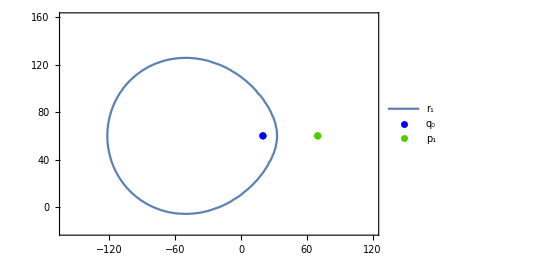

D:\study\phd_research\main\horsefly\viz_aid\2drones_q1.pdf

```mathematica
SetDirectory["D:\study\phd_research\main\horsefly\viz_aid"]
ClearAll["Global`*"]
q0 =Transpose@{{20},{60}};
p1 = Transpose@{{70},{60}};
plot1=ListPlot[q0, PlotStyle->Blue, PlotLegends->{Subscript[q,0]}];
plot2= ListPlot[p1, PlotStyle->{RGBColor[0.3,0.8,0]}, PlotLegends->{Subscript[p,1]}];
plot3= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0},
{x,-160,120},{y,-20,160},PlotLegends->{Subscript[r,1]}];
s = Show[plot3, plot1,plot2, AspectRatio->Automatic]
Export[Directory[] <> "\2drones_q1.pdf",s]
```

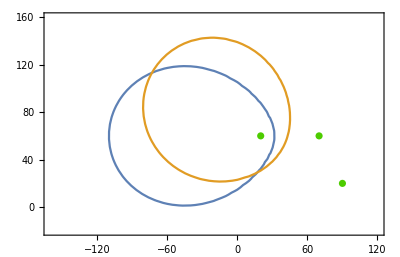

D:\study\phd_research\main\horsefly\viz_aid\3drones_left.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+2.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,160}];
s = Show[{plot2, plot1}, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_left.pdf",s]
```

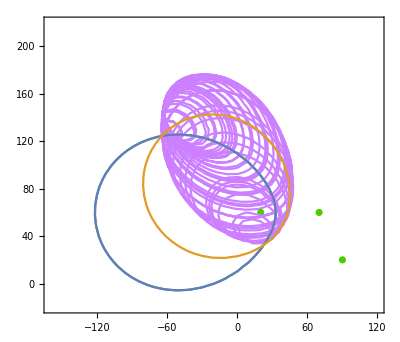

C:\Users\kienn\OneDrive\Documents\3drones_right.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
v0 = 10;
v1 = 12;
v2=  15;
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2 = ContourPlot[(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0,{x,-160,120},{y,-20,220}];
plot3= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,220}];
points=Cases[Normal@plot2,Line[pts_]->pts,Infinity];
Join@@points;(*if you don't want disjoint components to be separate*)
points = points[[1]];
t0 = 1.8;

(*xq = 31.79870818081344;
yq = 51.87059811623722;
Print[(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]];
ploti = ContourPlot[
(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]+
(1/v1)*Sqrt[(x-xq)^2+(y-yq)^2]-
(1/v2)*Sqrt[(x-90)^2+(y-20)^2]
==0,
{x,-160,160},{y,-40,160}];
s = Show[ploti, AspectRatio->Automatic]
*)

plotList = {};
Do[
xq = i[[1]];
yq= i[[2]];
ploti=ContourPlot[
(1/v1)Sqrt[(xq-70)^2+(yq-60)^2]+
(1/v1)Sqrt[(x-xq)^2+(y-yq)^2]-
(1/v2)Sqrt[(x-90)^2+(y-20)^2]
==0,
{x,-160,120},{y,-20,220}, ContourStyle->RGBColor[0.8,0.5,1]];
AppendTo[plotList,ploti];
,{i, points}]
PrependTo[plotList,plot1];
PrependTo[plotList,plot2];
AppendTo[plotList,plot3];
s = Show[plotList, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_center.pdf",s]
```

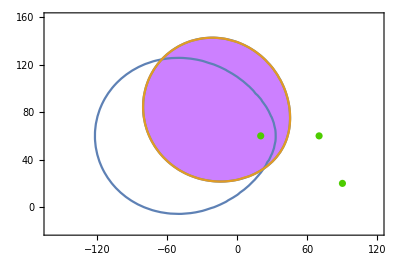

C:\Users\kienn\OneDrive\Documents\3drones_right.pdf

```mathematica
ClearAll["Global`*"]
xx={20, 70, 90};
yy ={60,60,20};
data=Transpose@{xx,yy};
plot1= ListPlot[data, PlotStyle->{RGBColor[0.3,0.8,0]}];
plot2= ContourPlot[
{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8==0, (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8==0},
{x,-160,120},{y,-20,160}];
plot3= RegionPlot[
{ (1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/15)Sqrt[(x-90)^2+(y-20)^2]+1.8<0},
{x,-160,120},{y,-20,160}, PlotStyle->RGBColor[0.8,0.5,1]];
s = Show[{plot3, plot2, plot1}, AspectRatio->Automatic]
Export[Directory[] <> "\3drones_right.pdf",s]
```

```mathematica
Show[List,AspectRatio->Automatic]
```

Show::gtype: Symbol is not a type of graphics.

```mathematica
Show[List,AspectRatio->Automatic]
```

Show::gtype: Symbol is not a type of graphics.

Show[List,AspectRatio→Automatic]

```mathematica
Plot3D[{(1/10)  Sqrt[(x-20)^2+(y-60)^2]-(1/12)Sqrt[(x-70)^2+(y-60)^2]+1.8, z=8},{x,-300,300},{y,-300,300},ColorFunction->"RustTones"]
```

-Graphics3D-